# Noise analysis of piezo controller

## Setup

```mathematica
(* keep mathematica from complaining in interpolating functions *)
Off[InterpolatingFunction::dmval]
Off[NIntegrate::ncvb]

(* set directory path *)
SetDirectory[NotebookDirectory[]];

(* constants, etc. *)
c=299792458;
kB=1.38064852*^-23;
hbar=1.0545718*^-34;
ϵ0=8.85418782*^-12;
a0=.52917721092*^-10;
e=1.602176487*^-19;
pp=1.*^-12;
nn=1.*^-9;
uu=1.*^-6;
mm=1.*^-3;
kk=1.*^3;
MM=1.*^6;
GG=1.*^9;

T=300; (* default temperature *)

(* parallel impedances *)
par[z1_,z2_]:=z1 z2/(z1+z2);
```

## LM7171 noise model

To pull in current and voltage noise from graph, do the following (although already done once; see coordinates & transformation below):

* Pull points off graph -- double click and select “coordinates tool”.
* {vy, vx, vo} are the coordinates of the y, x, and origin (axes), for coordinate transformation.
* Vcurve is a sequence of points from the curve itself. From that list of pixel coordinates, do a transformation to get into units of nV/rtHz.

```mathematica
VnoiseImg=Binarize[Import["LM7171VoltNoise.png"]];
InoiseImg=Binarize[Import["LM7171CurrNoise.png"]];
(* re-import images if necessary *)
```

```mathematica
GraphicsRow[{VnoiseImg,InoiseImg}]
```

-Graphics-

```mathematica
(* Points from graph *)
{vy,vx,vo}={{240,16},{723,499},{240,499}};
Vcurve={{723,466},{703,466},{678,464},{652,464},{628,461},{608,455},{590,446},{561,433},{523,413},{497,399},{464,381},{428,357},{406,339},{388,322},{366,297},{346,273},{315,233},{289,191},{269,160},{244,120}};

(* coordinate transformation; working in log units *)
Vtransform=FindGeometricTransform[{{0,1},{5,1},{0,3}},{vo,vx,vy}][[2]];
VptsLog=Vtransform@Vcurve;
(* VinterpolationLog is the voltage noise interpolating function *)
VinterpolationLog=Interpolation[VptsLog,InterpolationOrder->2];


(* now repeat for current noise *)
{iy,ix,io}={{184,9},{667,493},{184,493}};
Icurve={{666,452},{642,453},{615,453},{578,449},{550,443},{512,431},{476,415},{449,396},{426,375},{393,343},{375,326},{355,308},{329,284},{297,255},{283,241},{262,220},{247,205},{230,187},{201,155},{187,140}};

(* coordinate transformation; working in log units *)
Itransform=FindGeometricTransform[{{0,0},{5,0},{0,2}},{io,ix,iy}][[2]];
IptsLog=Itransform@Icurve;
IinterpolationLog=Interpolation[IptsLog,InterpolationOrder->2];

(* Finally, define functions *)
VVNoiseOpAmp[f_]:=(10^(VinterpolationLog[Log10[f]])nn)^2
IINoiseOpAmp[f_]:=(10^(IinterpolationLog[Log10[f]])pp)^2
```

### Check interpolating functions

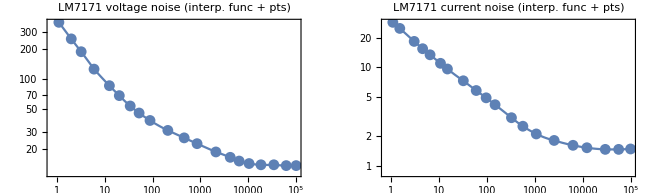

```mathematica
(* plot along with extracted points to make sure the interpolation worked ok *)
Vplt=ListLogLogPlot[Map[10^#&,VptsLog,{2}],Frame->True,GridLines->Automatic,PlotLabel->"LM7171 voltage noise (interp. func + pts)"];


Iplt=ListLogLogPlot[Map[10^#&,IptsLog,{2}],Frame->True,GridLines->Automatic, PlotLabel->"LM7171 current noise (interp. func + pts)"];

GraphicsRow[{Show[Vplt,LogLogPlot[√VVNoiseOpAmp[f]/nn,{f,1,10^5}]],
Show[Iplt,LogLogPlot[√IINoiseOpAmp[f]/pp,{f,1,10^5}]]}]
```

## DAC noise model

Using the AD5663R DAC,

```mathematica
DacNoiseImg=Binarize[Import["AD5663RVoltNoise.png"]]
(* re-import if necessary*)
```

-Graphics-

```mathematica
(* points from graph *)
{dy,dx,do}={{155,48},{903,645},{155,645}};
DACcurve={{893,604},{862,599},{833,598},{804,596},{760,592},{731,591},{711,591},{699,591},{671,591},{638,591},{604,589},{568,592},{545,589},{513,581},{487,577},{461,567},{443,557},{413,540},{396,527},{380,509},{366,489},{350,468},{344,456},{339,448},{331,420},{312,380},{291,346},{268,320},{249,300},{222,273},{194,248},{177,233},{157,218}};
(*coordinate transformation, working in log units only in x*)DACtransform=FindGeometricTransform[{{2,0},{7,0},{2,800}},{do,dx,dy}][[2]];
DACptsLog=DACtransform@DACcurve;
DACinterpolationLog=Interpolation[DACptsLog,InterpolationOrder->1];

VVNoiseDAC[f_]:=(DACinterpolationLog[Log10[f]]nn)^2
```

### Check interpolating function

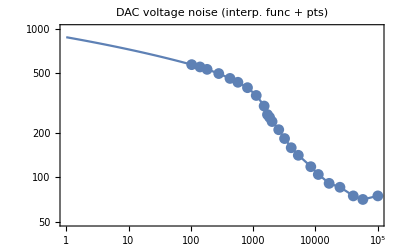

```mathematica
DACpts=Map[{10^#[[1]],#[[2]]}&,DACptsLog];
DACplt=ListLogLogPlot[DACpts,Frame->True,GridLines->Automatic,PlotLabel->"DAC voltage noise (interp. func + pts)", PlotRange->{{1,100kk},{50,1000}}];
Show[DACplt,LogLogPlot[√VVNoiseDAC[f]/nn,{f,1,100kk}]]
```

## DRV2700 Noise model

After the RC filter ladder, we’ve measured the DRV2700 noise spectrum (by measuring the spectrum of the control output of U2). We get the following (see python notebook for pre-processing):

```mathematica
DRVNoise=Import["DRVResidualNoise.png"];
DRVNoise
```

-Graphics-

```mathematica
{drvx,drvy,drvo}={{390,253},{55,30},{55,253}};
DRV50={{389,236},{381,236},{370,233},{361,225},{355,218},{353,205},{342,188},{331,179},{326,168},{315,155},{306,145},{297,136},{281,124},{272,117},{260,110},{247,101},{233,93},{219,86},{206,80},{186,78},{169,76},{151,78},{141,81},{130,88},{107,93}};
DRV100={{396,232},{394,232},{390,232},{385,231},{377,230},{369,225},{365,218},{363,211},{360,203},{357,195},{352,189},{347,183},{341,178},{335,173},{329,167},{321,162},{312,155},{305,150},{298,145},{290,140},{282,135},{275,130},{268,127},{261,122},{253,119},{245,115},{238,111},{231,110},{221,108},{211,107},{201,106},{193,106},{184,107},{172,108},{162,109},{152,109},{142,109},{127,109}}(*{{389,231},{382,231},{373,229},{366,218},{359,202},{348,190},{343,182},{331,171},{317,159},{300,149},{287,138},{271,128},{255,119},{237,111},{223,109},{199,106},{173,107},{148,109},{126,111},{107,123}}*);
DRV200={{401,231},{393,231},{386,229},{379,223},{369,214},{360,207},{351,203},{338,195},{328,190},{317,182},{307,177},{298,171},{286,165},{274,157},{262,152},{252,147},{243,145},{228,145},{217,145},{204,145},{195,146},{184,144},{173,142},{166,139},{155,135},{148,128},{140,128},{123,130},{107,130}};

DRVTransform=FindGeometricTransform[{{-1,-6},{4,-6},{-1,-1}},{drvo,drvx,drvy}][[2]];

DRV50Log=DRVTransform@DRV50;
DRV50InterpolationLog=Interpolation[DRV50Log,InterpolationOrder->1];

DRV100Log=DRVTransform@DRV100;
DRV100InterpolationLog=Interpolation[DRV100Log,InterpolationOrder->2];

DRV200Log=DRVTransform@DRV200;
DRV200InterpolationLog=Interpolation[DRV200Log,InterpolationOrder->1];

VVNoiseDRV50[f_]:=(10^(DRV50InterpolationLog[Log10[f]]))^2
VVNoiseDRV100[f_]:=(10^(DRV100InterpolationLog[Log10[f]]))^2
VVNoiseDRV200[f_]:=(10^(DRV200InterpolationLog[Log10[f]]))^2
```

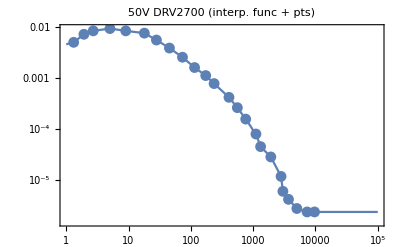

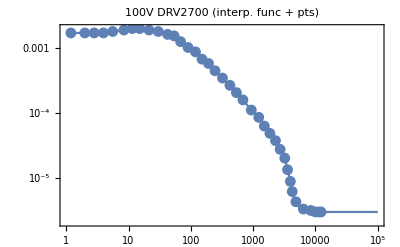

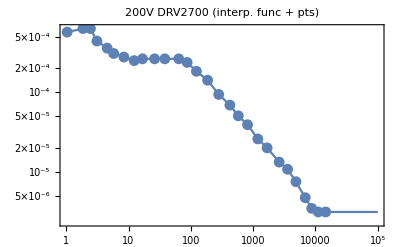

```mathematica
Show[ListLogLogPlot[Map[10^#&,DRV50Log,{2}],Frame->True,GridLines->Automatic, PlotLabel->"50V DRV2700 (interp. func + pts)",PlotRange->{{1,100kk},All}],LogLogPlot[√VVNoiseDRV50[f],{f,1,100kk}]]

Show[ListLogLogPlot[Map[10^#&,DRV100Log,{2}],Frame->True,GridLines->Automatic, PlotLabel->"100V DRV2700 (interp. func + pts)",PlotRange->{{1,100kk},All}],LogLogPlot[√VVNoiseDRV100[f],{f,1,100kk}]]


Show[ListLogLogPlot[Map[10^#&,DRV200Log,{2}],Frame->True,GridLines->Automatic, PlotLabel->"200V DRV2700 (interp. func + pts)",PlotRange->{{1,100kk},All}],LogLogPlot[√VVNoiseDRV200[f],{f,1,100kk}]]
(*Plot[VVNoiseDRV50[f]*)
```

## Noise Calculations

We start with our noise model, and will calcualte everything referred to output.

```mathematica
NoiseModel=Import[ParentDirectory[]<>"/fig/NoiseModel.ai"]//First;
Show[NoiseModel]
```

-Graphics-

```mathematica
(* Values *)
R1=1MM;
C1=1nn;
R2=20.5kk;
Rmod=1MM;
Cmod=1nn;
Rlp=20.5kk;

(* effective Z -- see full circuit for details -- Ron resistance is 0.7 ohms for part*)
Zlp[f_]:=par[par[(1/(2Pi I f 10uu)+0.7),1/(2Pi I f 47nn)],1MM];

Z1[f_]:=par[R1,1/(2Pi I f C1)];
Z2[f_]:=R2;
Zmod[f_]:=par[Rmod,1/(2Pi I f Cmod)];

Zpos[f_]:=par[Rlp,Zlp[f]];
```

```mathematica
(*Gains*)
GInv[f_]:=-Z1[f]/par[Z2[f], Zmod[f]];
GNonInv[f_]:=1+Z1[f]/par[Z2[f],Zmod[f]];
GMod[f_]:=-Z1[f]/Zmod[f];
G2[f_]:=-Z1[f]/Z2[f];
GCtl[f_]:=Zlp[f]/(Rlp+Zlp[f])GNonInv[f];
```

Now, we calculate the RTO voltage noise power spectral densities (V^2/Hz).

```mathematica
(* First term in inverting node current noise; transimpedance gain to output *)
(* second term is non-inverting node; transimpedance gain is impedance*GNonInv *)
(* take Re[..] to ditch numerical errors leading to imaginary component *)
OpAmpII[f_]:=Re[IINoiseOpAmp[f](Z1[f]Conjugate[Z1[f]])+
IINoiseOpAmp[f](Zpos[f]GNonInv[f]Conjugate[Zpos[f]GNonInv[f]])];

OpAmpVV[f_]:=Re[VVNoiseOpAmp[f](GNonInv[f]Conjugate[GNonInv[f]])];

DacVV[f_]:=Re[VVNoiseDAC[f]GCtl[f]Conjugate[GCtl[f]]];
```

For the Johnson noise, we have to be a little careful! The generalized voltage noise (for complex impedance noise source) is 4 k_B T Re[Z]. But, at the inverting node, those get gained differently. Voltage noise across Z1 appears directly at the output. Voltage noise across Zmod sees a gain of GMod (=1 in our case). Voltage noise across R2 sees a gain of G2 = Z1/R2.

We could equivalently treat each noise as a parallel current across the resistor only -- this gives the same results, where we use the transimpedance gain Z1 seen from the inverting node of U2.

```mathematica
(* Contributions from {Z1, R2, Zmod,{ Zlp, Rlp}} *) 
JohnsonVV[f_]:=Re[4 kB T(Re[Z1[f]]+
Re[Zmod[f]]GMod[f]Conjugate[GMod[f]]+
R2 G2[f]Conjugate[G2[f]]+
Re[par[Zlp[f],Rlp]]GNonInv[f]Conjugate[GNonInv[f]]
)];

(* alternative calculation method, taking noise source to be currents in parallel with resistors...*)
JohnsonVV2[f_]:=Re[4 kB T((1/R1+1/Rmod+1/R2)Z1[f]Conjugate[Z1[f]]+
Zpos[f]GNonInv[f]Conjugate[Zpos[f]GNonInv[f]](1/Rlp+1/(1MM))
)];
```

We now double check these are the same... Note, including the 1MM resistor in parallel with Clp doesn’t appreciably change the result; thus it is left out of the analysis in the paper for simplicity.

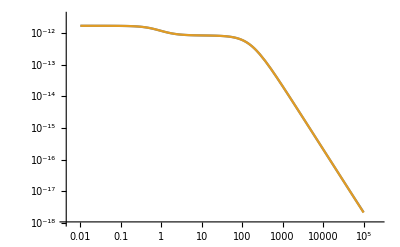

```mathematica
LogLogPlot[{JohnsonVV[f],JohnsonVV2[f]},{f,.01,100kk}]
```

For v_(n,DRV), we have to create an open-loop gain model for the op amp. It has an open loop gain of 85dB, with dominant pole at 10kHz (from datasheet). Thus, we do:

{0.000157842,{f→6351.98}}

Minimum in GDrv: {0.000157842,{f→6351.98}}

Attenuation in dB: -76.0355

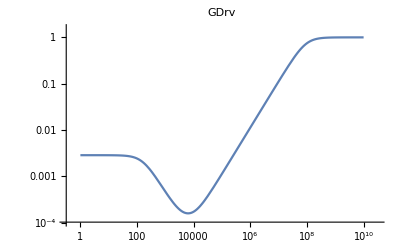

Averaged supression from 1Hz - 100kHz: -76.5969 dB

-------------------------------------------------

Resid DRV2700 noise at 50V: 51.1578 mVrms

Resid DRV2700 noise at 100V: 18.361 mVrms

Resid DRV2700 noise at 200V: 3.77373 mVrms

```mathematica
GOpenLoop[f_]:=10^(85/20.)/(1+I f/(10kk));
ReverseTransfer[f_]:=par[Z2[f],Zmod[f]]/(Z1[f]+par[Z2[f],Zmod[f]]);
(* gain seen by output node *)
GDrv[f_]:=1/(1+GOpenLoop[f]ReverseTransfer[f]);

(* find the max attenuation due ot GDrv, in dB *)
min=NMinimize[{Abs[GDrv[f]],f>0},f∈Reals]
Print["Minimum in GDrv: ", min]
Print["Attenuation in dB: ", 20 Log10[First[min]]]

DRV50VV[f_]:=Re[GDrv[f]Conjugate[GDrv[f]]VVNoiseDRV50[f]];
DRV100VV[f_]:=Piecewise[{{Re[GDrv[f]Conjugate[GDrv[f]]VVNoiseDRV100[f]],f≤10kk},{0,f>10kk}}];
DRV200VV[f_]:=Piecewise[{{Re[GDrv[f]Conjugate[GDrv[f]]VVNoiseDRV200[f]],f≤10kk},{0,f>10kk}}];

LogLogPlot[Abs[GDrv[f]],{f,1,10GG}, PlotLabel->"GDrv"]

(* compute the "average" noise suppression over bandwidth 1Hz-100kHz; not sure if meaningful though *)
Sqrt[NIntegrate[Abs[GDrv[f]]^2,{f,1,10kk}]/(100kk-1)];
Print["Averaged supression from 1Hz - 100kHz: ", 20 Log10[%], " dB"]
Print["-------------------------------------------------"]

(* residual noise; neglecting > 10kHz since negligible and below noise floor of measurement *)

ResidNoise50V=√NIntegrate[VVNoiseDRV50[f],{f,1,10kk}];
ResidNoise100V=√NIntegrate[VVNoiseDRV100[f],{f,1,10kk}];
ResidNoise200V=√NIntegrate[VVNoiseDRV200[f],{f,1,10kk}];
Print["Resid DRV2700 noise at 50V: ", ResidNoise50V/mm, " mVrms"];
Print["Resid DRV2700 noise at 100V: ", ResidNoise100V/mm, " mVrms"];
Print["Resid DRV2700 noise at 200V: ", ResidNoise200V/mm, " mVrms"];
```

We measured and use the residual noise of the DRV2700 as our noise source.

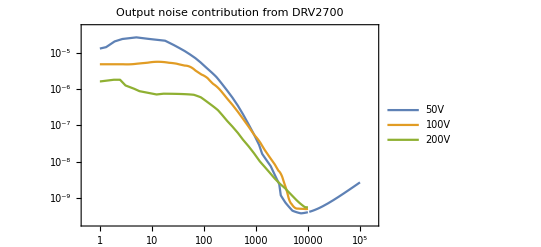

Residual DRV2700 noise, v_(n, DRV), @50V: 51.1578 mVrms

Residual DRV2700 noise, v_(n, DRV), @100V: 18.361 mVrms

Residual DRV2700 noise, v_(n, DRV), @200V: 3.77373 mVrms

```mathematica
LogLogPlot[{√DRV50VV[f],√DRV100VV[f],√DRV200VV[f]},{f,1,100kk},PlotLegends->{"50V","100V","200V"},Frame->True,PlotLabel->"Output noise contribution from DRV2700"]

(* again, sanity check: *)
Print["Residual DRV2700 noise, v_(n, DRV), @50V: ",√NIntegrate[VVNoiseDRV50[f] (*GDrv[f] Conjugate[GDrv[f]]*),{f,1,10kk}]/mm," mVrms"]
Print["Residual DRV2700 noise, v_(n, DRV), @100V: ",√NIntegrate[VVNoiseDRV100[f] (*GDrv[f] Conjugate[GDrv[f]]*),{f,1,10kk}]/mm," mVrms"]
Print["Residual DRV2700 noise, v_(n, DRV), @200V: ",√NIntegrate[VVNoiseDRV200[f] (*GDrv[f] Conjugate[GDrv[f]]*),{f,1,10kk}]/mm," mVrms"]
```

Now, for the total RMS noise after the op amp:

```mathematica
Print["DRV2700 noise contrib. @50V: ",√NIntegrate[DRV50VV[f],{f,1,100kk}]/uu," uVrms"]
Print["DRV2700 noise contrib. @100V: ",√NIntegrate[DRV100VV[f],{f,1,100kk}]/uu," uVrms"]
Print["DRV2700 noise contrib. @200V: ",√NIntegrate[DRV200VV[f],{f,1,100kk}]/uu," uVrms"]
```

DRV2700 noise contrib. @50V: 138.339 uVrms

DRV2700 noise contrib. @100V: 45.3065 uVrms

DRV2700 noise contrib. @200V: 8.45448 uVrms

## Results

We have the following contributions (assuming 100V output):

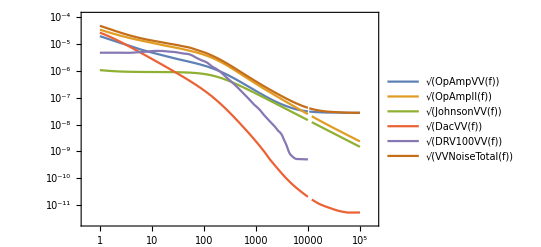

Total noise (100V out), 1-10Hz: 65.8809 uVrms

Total noise (100V out), 10Hz-100kHz: 91.9661 uVrms

Total noise (100V out), 1-100kHz: 113.13 uVrms

------------------------------

OpAmp volt noise, 1-10Hz: 26.3067 uVrms

OpAmp volt noise, 10Hz-100kHz: 31.4702 uVrms

OpAmp volt noise, 1-100kHz: 41.0167 uVrms

------------------------------

OpAmp Curr noise, 1-10Hz: 51.2959 uVrms

OpAmp Curr noise, 10Hz-100kHz: 73.361 uVrms

OpAmp Curr noise, 1-100kHz: 89.5163 uVrms

------------------------------

DAC noise, 1-10Hz: 27.8791 uVrms

DAC noise, 10Hz-100kHz: 7.9458 uVrms

DAC noise, 1-100kHz: 28.9893 uVrms

------------------------------

Johnson noise, 1-10Hz: 2.82127 uVrms

Johnson noise, 10Hz-100kHz: 14.2047 uVrms

Johnson noise, 1-100kHz: 14.4822 uVrms

------------------------------

DRV residual noise, 200V, 1-10Hz: 3.4191 uVrms

DRV residual noise, 200V, 10Hz-100kHz: 7.72676 uVrms

DRV residual noise, 200V, 1-100kHz: 8.45448 uVrms

------------------------------

DRV residual noise, 100V, 1-10Hz: 15.224 uVrms

DRV residual noise, 100V, 10Hz-100kHz: 42.6688 uVrms

DRV residual noise, 100V, 1-100kHz: 45.3065 uVrms

------------------------------

DRV residual noise, 50V, 1-10Hz: 71.8863 uVrms

DRV residual noise, 50V, 10Hz-100kHz: 118.187 uVrms

DRV residual noise, 50V, 1-100kHz: 138.339 uVrms

------------------------------

Total Noise (different outputs); 50V, 1-100kHz: 172.868uVrms

100V, 1-100kHz: 113.13uVrms

200V, 1-100kHz: 104.005uVrms

```mathematica
VVNoiseTotal[f_]:=OpAmpII[f]+OpAmpVV[f]+DacVV[f]+JohnsonVV[f]+DRV100VV[f];
noiseplot=LogLogPlot[{√OpAmpVV[f],√OpAmpII[f],√JohnsonVV[f],√DacVV[f],√DRV100VV[f],√VVNoiseTotal[f]},{f,1,100kk},PlotLegends->"Expressions",Frame->True];
exportTable=Table[{f,√OpAmpVV[f],√OpAmpII[f],√JohnsonVV[f],√DacVV[f],√DRV100VV[f],√VVNoiseTotal[f]}/.f->10^s,{s,0,5,.05}];
Export["data/CalcNoiseContrib.csv",exportTable];
Show[noiseplot]
Print["Total noise (100V out), 1-10Hz: ",√NIntegrate[VVNoiseTotal[f],{f,1,10}]/uu," uVrms"]
Print["Total noise (100V out), 10Hz-100kHz: ",√NIntegrate[VVNoiseTotal[f],{f,10,100kk}]/uu," uVrms"]
Print["Total noise (100V out), 1-100kHz: ",√NIntegrate[VVNoiseTotal[f],{f,1,100kk}]/uu," uVrms"]
Print["------------------------------"]
Print["OpAmp volt noise, 1-10Hz: ",√NIntegrate[OpAmpVV[f],{f,1,10}]/uu," uVrms"]
Print["OpAmp volt noise, 10Hz-100kHz: ",√NIntegrate[OpAmpVV[f],{f,10,100kk}]/uu," uVrms"]
Print["OpAmp volt noise, 1-100kHz: ",√NIntegrate[OpAmpVV[f],{f,1,100kk}]/uu," uVrms"]
Print["------------------------------"]
Print["OpAmp Curr noise, 1-10Hz: ",√NIntegrate[OpAmpII[f],{f,1,10}]/uu," uVrms"]
Print["OpAmp Curr noise, 10Hz-100kHz: ",√NIntegrate[OpAmpII[f],{f,10,100kk}]/uu," uVrms"]
Print["OpAmp Curr noise, 1-100kHz: ",√NIntegrate[OpAmpII[f],{f,1,100kk}]/uu," uVrms"]
Print["------------------------------"]
Print["DAC noise, 1-10Hz: ",√NIntegrate[DacVV[f],{f,1,10}]/uu," uVrms"]
Print["DAC noise, 10Hz-100kHz: ",√NIntegrate[DacVV[f],{f,10,100kk}]/uu," uVrms"]
Print["DAC noise, 1-100kHz: ",√NIntegrate[DacVV[f],{f,1,100kk}]/uu," uVrms"]
Print["------------------------------"]
Print["Johnson noise, 1-10Hz: ",√NIntegrate[JohnsonVV[f],{f,1,10}]/uu," uVrms"]
Print["Johnson noise, 10Hz-100kHz: ",√NIntegrate[JohnsonVV[f],{f,10,100kk}]/uu," uVrms"]
Print["Johnson noise, 1-100kHz: ",√NIntegrate[JohnsonVV[f],{f,1,100kk}]/uu," uVrms"]
Print["------------------------------"]
Print["DRV residual noise, 200V, 1-10Hz: ",√NIntegrate[DRV200VV[f],{f,1,10}]/uu," uVrms"]
Print["DRV residual noise, 200V, 10Hz-100kHz: ",√NIntegrate[DRV200VV[f],{f,10,100kk}]/uu," uVrms"]
Print["DRV residual noise, 200V, 1-100kHz: ",√NIntegrate[DRV200VV[f],{f,1,100kk}]/uu," uVrms"]
Print["------------------------------"]
Print["DRV residual noise, 100V, 1-10Hz: ",√NIntegrate[DRV100VV[f],{f,1,10}]/uu," uVrms"]
Print["DRV residual noise, 100V, 10Hz-100kHz: ",√NIntegrate[DRV100VV[f],{f,10,100kk}]/uu," uVrms"]
Print["DRV residual noise, 100V, 1-100kHz: ",√NIntegrate[DRV100VV[f],{f,1,100kk}]/uu," uVrms"]
Print["------------------------------"]
Print["DRV residual noise, 50V, 1-10Hz: ",√NIntegrate[DRV50VV[f],{f,1,10}]/uu," uVrms"]
Print["DRV residual noise, 50V, 10Hz-100kHz: ",√NIntegrate[DRV50VV[f],{f,10,100kk}]/uu," uVrms"]
Print["DRV residual noise, 50V, 1-100kHz: ",√NIntegrate[DRV50VV[f],{f,1,100kk}]/uu," uVrms"]

Print["------------------------------\n\n"]

Print["Total Noise (different outputs); 50V, 1-100kHz: ",√NIntegrate[OpAmpII[f]+OpAmpVV[f]+DacVV[f]+JohnsonVV[f]+DRV50VV[f],{f,1,100kk}]/uu, "uVrms"]

Print["100V, 1-100kHz: ",√NIntegrate[OpAmpII[f]+OpAmpVV[f]+DacVV[f]+JohnsonVV[f]+DRV100VV[f],{f,1,100kk}]/uu, "uVrms"]

Print["200V, 1-100kHz: ",√NIntegrate[OpAmpII[f]+OpAmpVV[f]+DacVV[f]+JohnsonVV[f]+DRV200VV[f],{f,1,100kk}]/uu, "uVrms"]
```